```mathematica
Exit[]
```

```mathematica
Needs["PM`"]
UninstallPackages[$PM,{"KnotToolsLink"}];
ClearAllCache[$PM];
LoadPackages[{"Geometries","KnotToolsLink"}]
```

Deleting package KnotToolsLink.

Deleting installation path.

WARNING: LTemplate has not yet been tested with Mathematica 14.1.0.
The latest supported Mathematica version is 12.3.1.
Please report any issues you find to szhorvat at gmail.com.

Updating package KnotToolsLink...

/Users/jasoncantarella/Dropbox/Jason/PackageSources_2024-10-17T14:29:03/PackageSources/KnotToolsLink/LibrarySources/PlanarDiagramObject/

Exporting library PlanarDiagramObject to /Users/jasoncantarella/Library/Wolfram/Applications/KnotToolsLink/LibraryResources/Source.

Names of functions in library PlanarDiagramObject are made public.

Current directory is: /Users/jasoncantarella/Library/Wolfram/Applications/KnotToolsLink/LibraryResources/Source

Unloading library PlanarDiagramObject ...

Generating library code ...

Compiling library code ...

Compilation done. Time elapsed = 16.2916

```mathematica
(*Exit[]*)
```

```mathematica
(*Most of the time you do not have to recompile. Then load the package like this is faster.*)
Needs["PM`"]
LoadPackages[{"Geometries","KnotToolsLink"}]
```

WARNING: LTemplate has not yet been tested with Mathematica 14.1.0.
The latest supported Mathematica version is 12.3.1.
Please report any issues you find to szhorvat at gmail.com.

```mathematica
hardknotfiles=FileNames[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"data","diagrams","hardunknots","*.tsv"}]];
```

```mathematica
PD=PlanarDiagram[Import[Echo[hardknotfiles[[18]]]],0]
```

/Users/jasoncantarella/KnotTools/data/diagrams/hardunknots/PZ31.tsv

PlanarDiagramObject[…]

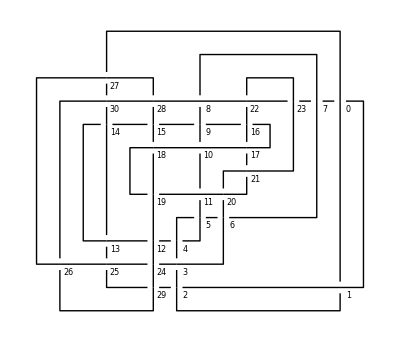

```mathematica
PlotDiagram[PD]
```

```mathematica
PD1=SimplifyDiagram4[PD]
```

PlanarDiagramObject[…]

```mathematica
ReginaHOMFLY[PDCode[PD]][L,M]
```

ReginaHOMFLY: time elapsed→0.12088

1

```mathematica
PDSnaPy=SnapPySymplifyPickup[PDCode[PD]]
```

0.457258 s elapsed while compiling PDCodeAppendSign.

Writing to /Users/jasoncantarella/Library/Wolfram/Applications/KnotToolsLink/LibraryResources/MacOSX-ARM64/PDCodeAppendSign.dylib.

<|PDCode→{{56,48,57,47,1},{46,56,47,55,1},{54,46,55,45,1},{44,13,45,14,-1},{34,44,35,43,1},{42,36,43,35,1},{41,15,42,14,1},{57,40,58,41,-1},{39,60,40,61,-1},{29,39,30,38,1},{37,27,38,26,1},{36,23,37,24,-1},{33,4,34,5,-1},{51,32,52,33,-1},{31,50,32,51,-1},{30,8,31,7,1},{28,19,29,20,-1},{20,27,21,28,-1},{6,26,7,25,1},{24,6,25,5,1},{15,22,16,23,-1},{21,16,22,17,-1},{18,60,19,59,1},{58,18,59,17,1},{12,3,13,4,-1},{52,11,53,12,-1},{1,10,2,11,-1},{48,10,49,9,1},{8,61,9,0,-1},{53,2,54,3,-1},{49,1,50,0,1}},Timing→0.008462,Method→SnapPySymplifyPickup|>

```mathematica
PDRegina=ReginaSimplify[PDCode[PD]]
```

<|PDCode→{{0,50,1,49,1},{3,11,4,10,1},{5,33,6,32,1},{6,43,7,44,-1},{8,20,9,19,1},{9,22,10,23,-1},{12,2,13,1,1},{13,52,14,53,-1},{14,39,15,40,-1},{15,37,16,36,1},{16,8,17,7,1},{17,26,18,27,-1},{21,39,22,38,1},{24,29,25,30,-1},{25,18,26,19,-1},{27,45,28,44,1},{30,23,31,24,-1},{33,40,34,41,-1},{35,42,36,43,-1},{37,21,38,20,1},{41,34,42,35,-1},{45,29,46,28,1},{46,31,47,32,-1},{47,4,48,5,-1},{48,0,49,53,1},{50,11,51,12,-1},{51,3,52,2,1}},Timing→0.002019,Method→ReginaSimplify|>

```mathematica
PlotDiagram[PD]
```

-Graphics-

We’re going to assign a variable to each edge, giving the height of the edge as it leaves the crossing. We assume that edges stay at the same height through a crossing, so each arcline is going to need to access two heights; one as it leaves a crossing and the next arc in line’s height as it leaves the subsequent crossing. The quadratic objective function is just going to be the graph Laplacian of the cycle graph with 2n edges.  For each {a, b, c, d} in the PD code, we know that a is the incoming lower edge, c is the outgoing lower edge, and b and d are the overstrand, so we start by identifying these:

```mathematica
OutStrands[{a_,b_,c_,d_}]:= <|"under"->c,"over"->If[(b-d)^2==1,Max[{b,d}],Min[{b,d}]]|>;
```

Now we can set up a line in the constraint matrix so that when we dot it by vector of heights, the height associated with the overstrand is larger. We note that these matrix indices are offset by 1 from the edges they represent.

```mathematica
ConstraintLine[x_,r_]:={{r[[1]],#["under"]+1}->-1,{r[[1]],#["over"]+1}->+1}&@OutStrands[x[[1;;4]]] ;
```

```mathematica
BuildConstraintMatrix[PD_] := 
SparseArray[Flatten[
MapIndexed[
ConstraintLine,PD],
1],
{Length[PD],2Length[PD]}];
```

```mathematica
BuildConstraintMatrix[PDCode[PD]]
```

SparseArray[…]

```mathematica
BuildObjectiveFunction[PD_] :=SparseArray[((#.#)&@KirchhoffMatrix[CycleGraph[2*Length[PD]]]) + 0.1IdentityMatrix[2*Length[PD]]]
```

```mathematica
BuildObjectiveFunction[PDCode[PD]]
```

SparseArray[…]

```mathematica
Timing[SuggestedLevels = QuadraticOptimization[BuildObjectiveFunction[PDCode@PD],{BuildConstraintMatrix[PDCode@PD],ConstantArray[-2,Length[PDCode@PD]]}];]
```

{0.055102,Null}

We now check that we’ve correctly encoded the constraints by checking that at each crossing the difference between the outgoing arcs obeys the condition:

```mathematica
LevelsFunctionOkQ[PD_,f_]:= And @@(f[[#["over"]+1]]-f[[#["under"]+1]] >= 2 & /@ (OutStrands /@ PD[[All,1;;4]]))
```

```mathematica
LevelsFunctionOkQ[PDCode[PD],SuggestedLevels]
```

True

So far, so good.

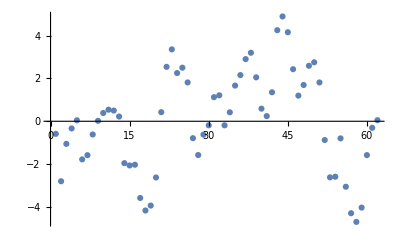

```mathematica
ListPlot[SuggestedLevels]
```

Here’s an experiment: what if we standardized the data by sort order to avoid different points being too close to each other.

```mathematica
DiscreteLevels = 2*Flatten[Values@ KeySort@PositionIndex[Sort[MapIndexed[{#1,#2[[1]]}&,SuggestedLevels]][[All,2]]],1];
```

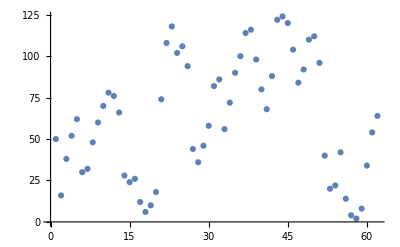

```mathematica
ListPlot[DiscreteLevels]
```

Now we need to construct new geometry according to the Levels embedding. We’ll need the ArcLines associated to the diagram. The strategy is to add a vertical segment to the curve at the first corner (or failing that, in the middle of the arc) which connects the levels at the start and end of the arc. So ArcLine[i] should be the line corresponding to edge i in the PD code (assuming that we’ve run CompressDiagramInPlace recently):

The value L[[i+1]] is the height of edge i at it’s outgoing crossing. L[[i+2]] is the height at the incoming crossing. We’ll make a new association which assigns this pair to each edge index.

```mathematica
ProcessArcLine[a_] := If[Length[a]==2,
{a[[1]],Mean[a],Mean[a],a[[2]]},
Join[a[[1;;2]],a[[2;;]]]]
```

```mathematica
LevelsEmbedding[PD_,L_]:= Block[{augmentedArcLines,al,procL,Lm=2,almost,edgeHeights},
edgeHeights = Association@MapIndexed[First[#2]-1->#1&,Transpose[{L,RotateLeft[L]}]];
al =  ProcessArcLine /@(Round[#,10]&/@ArcLines@Spherogram@PD);
Append[#,First[#]]&@DeleteDuplicates@Flatten[Table[
Join[
Append[edgeHeights[i][[1]]]/@al[i][[1;;2]],Append[edgeHeights[i][[2]]]/@al[i][[3;;]]
],{i,0,Length[L]-1} 
],1]
]
```

```mathematica
Graphics3D[Tube[LevelsEmbedding[PD,20*SuggestedLevels],1.0],ViewPoint->Top,ViewProjection->"Orthographic",ViewVertical->{0, 0, 1}]
```

-Graphics3D-

```mathematica
PlotDiagram[PD]
```

-Graphics-

Now we need to rotate this to get some new perspectives on everything. If we just choose left or right we’ll have a lot of edges disappear. So we need to rotate to a “generic” view. First, we try something that’s very close to the z-projection.

```mathematica
A ={{1.,0.,0.},{0.,1.,0.},{0.134,0.2987,1}};
```

```mathematica
Graphics3D[Tube[LevelsEmbedding[PD,10*SuggestedLevels].A,1.0],ViewPoint->Top,ViewProjection->"Orthographic",ViewVertical->{0, 0, 1}]
```

-Graphics3D-

```mathematica
CheckPD = PlanarDiagram[10.0*LevelsEmbedding[PD,SuggestedLevels].A]
```

PlanarDiagramObject[…]

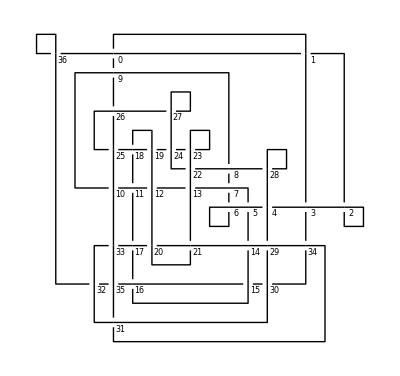

```mathematica
PlotDiagram[CheckPD]
```

```mathematica
PlotDiagram[SimplifyDiagram4[CheckPD]]
```

-Graphics-

```mathematica
CompressDiagramInPlace[CheckPD]
```

```mathematica
ReginaHOMFLY[PDCode[CheckPD]]
```

ReginaHOMFLY: time elapsed→0.118402

Function[{x,y},1]

```mathematica
R = RandomVariate[CircularRealMatrixDistribution[3]]
```

{{-0.68635,-0.69682,-0.208244},{-0.518578,0.268153,0.811893},{-0.509902,0.665234,-0.545403}}

```mathematica
Graphics3D[Tube[LevelsEmbedding[PD,30.0*SuggestedLevels].R,1],ViewPoint->Above]
```

-Graphics3D-

```mathematica
NewPD = PlanarDiagram[LevelsEmbedding[PD,10*SuggestedLevels].R]
```

PlanarDiagramObject[…]

```mathematica
(*Should be obsolete.*)
CompressDiagramInPlace[NewPD]
```

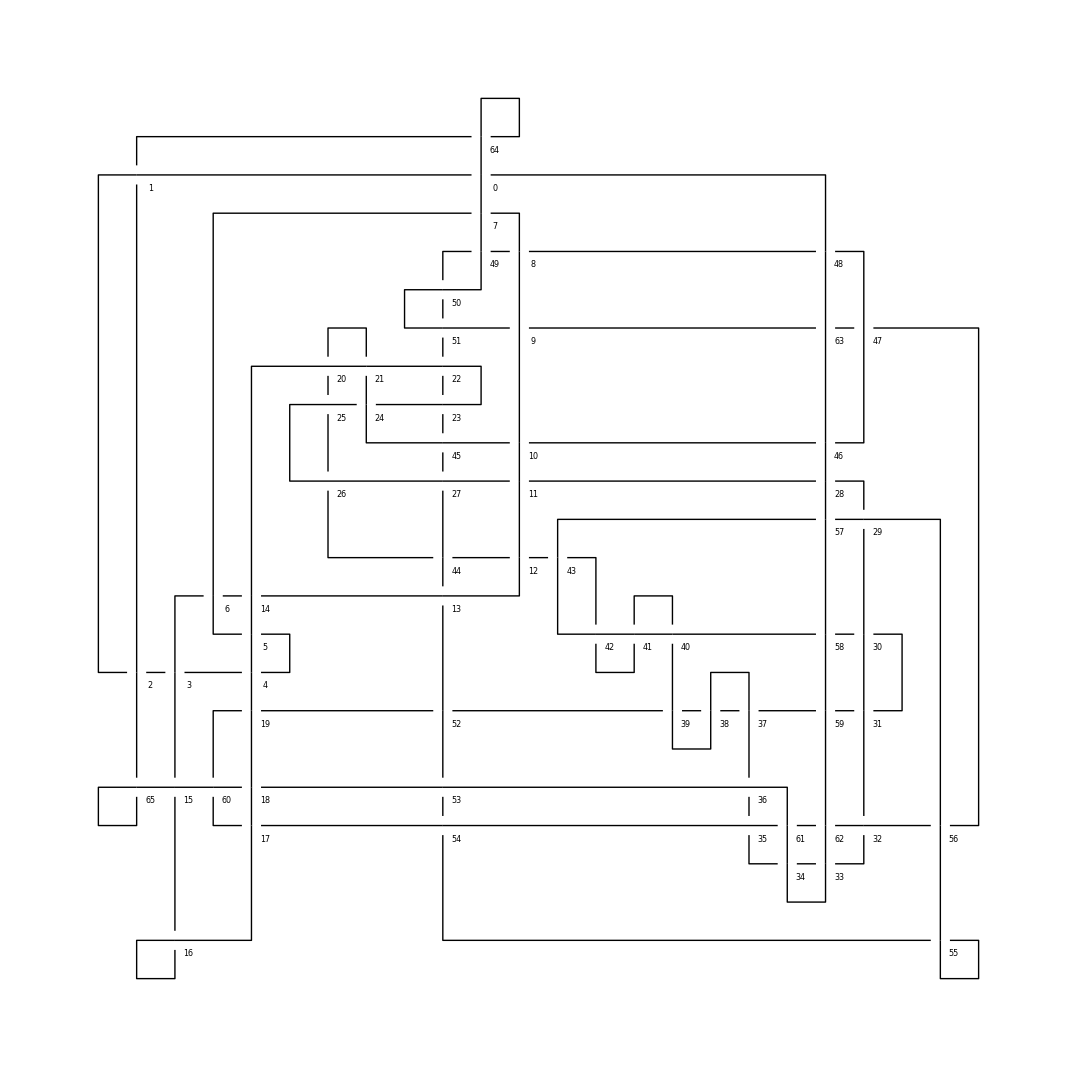

```mathematica
PlotDiagram[NewPD]
```

```mathematica
NewPDSimplified = SimplifyDiagram4[NewPD]
```

PlanarDiagramObject[…]

Nice! Ok, now we’re going to sew this together into a function that I can iterate:

```mathematica
LevelsSimplify[PD_]:= Block[{Lf,R,NewPD,SimplifiedNewPD,Dlf},
Lf = QuadraticOptimization[BuildObjectiveFunction[PDCode@PD],{BuildConstraintMatrix[PDCode@PD],ConstantArray[-2,Length[PDCode@PD]]}];
Dlf = 2*Flatten[Values@ KeySort@PositionIndex[Sort[MapIndexed[{#1,#2[[1]]}&,Lf]][[All,2]]],1];
R = RandomVariate[CircularRealMatrixDistribution[3]];
NewPD = PlanarDiagram[LevelsEmbedding[PD,30*Lf].R];
SimplifyDiagram4[NewPD]
]
```

Ok, so now we’re going to rerun the original Levels experimental knot:

```mathematica
PDlevels = PlanarDiagramUnsigned[{{425,137,0,136},{137,1,138,0},{1,135,2,134},{2,144,3,143},{3,127,4,126},{127,5,128,4},{58,5,59,6},{171,7,172,6},{148,8,149,7},{8,72,9,71},{70,10,71,9},{10,164,11,163},{164,12,165,11},{17,13,18,12},{68,13,69,14},{14,168,15,167},{168,16,169,15},{69,17,70,16},{18,166,19,165},{19,185,20,184},{25,21,26,20},{21,25,22,24},{41,23,42,22},{23,43,24,42},{26,183,27,184},{27,162,28,163},{149,28,150,29},{29,178,30,179},{30,174,31,173},{174,32,175,31},{32,176,33,175},{52,34,53,33},{47,34,48,35},{35,152,36,153},{155,36,156,37},{37,156,38,157},{159,38,160,39},{39,46,40,47},{40,182,41,181},{182,44,183,43},{44,161,45,162},{160,45,161,46},{151,49,152,48},{49,151,50,150},{177,51,178,50},{51,177,52,176},{53,181,54,180},{57,55,58,54},{55,129,56,128},{129,57,130,56},{146,60,147,59},{60,74,61,73},{120,61,121,62},{62,117,63,118},{66,63,67,64},{64,120,65,119},{118,66,119,65},{166,68,167,67},{169,72,170,73},{145,74,146,75},{75,144,76,145},{76,122,77,121},{86,78,87,77},{78,89,79,90},{88,79,89,80},{403,80,404,81},{394,82,395,81},{82,399,83,400},{398,83,399,84},{84,394,85,393},{85,404,86,405},{90,88,91,87},{366,91,367,92},{357,93,358,92},{93,357,94,356},{355,95,356,94},{95,355,96,354},{96,375,97,376},{376,97,377,98},{98,377,99,378},{378,99,379,100},{385,101,386,100},{101,387,102,386},{329,102,330,103},{103,330,104,331},{331,104,332,105},{322,105,323,106},{106,327,107,328},{107,320,108,321},{353,109,354,108},{109,351,110,350},{113,111,114,110},{111,352,112,353},{351,112,352,113},{114,339,115,340},{360,116,361,115},{116,360,117,359},{122,424,123,423},{138,124,139,123},{124,134,125,133},{125,143,126,142},{130,416,131,415},{414,132,415,131},{141,133,142,132},{135,425,136,424},{190,140,191,139},{140,190,141,189},{147,170,148,171},{153,158,154,159},{157,154,158,155},{179,173,180,172},{198,185,199,186},{186,195,187,196},{187,412,188,413},{188,420,189,419},{191,407,192,406},{192,421,193,422},{410,193,411,194},{194,409,195,410},{196,418,197,417},{416,198,417,197},{199,339,200,338},{239,200,240,201},{201,234,202,235},{251,203,252,202},{226,204,227,203},{204,272,205,271},{205,285,206,284},{257,207,258,206},{207,259,208,258},{208,281,209,282},{209,262,210,263},{269,210,270,211},{211,270,212,271},{253,212,254,213},{278,213,279,214},{214,255,215,256},{260,215,261,216},{216,259,217,260},{217,257,218,256},{218,289,219,290},{288,219,289,220},{220,287,221,288},{286,221,287,222},{222,285,223,286},{223,272,224,273},{249,224,250,225},{225,250,226,251},{252,227,253,228},{228,278,229,277},{229,290,230,291},{273,231,274,230},{248,231,249,232},{313,232,314,233},{233,314,234,315},{235,334,236,335},{335,236,336,237},{237,336,238,337},{337,238,338,239},{319,240,320,241},{241,318,242,319},{317,242,318,243},{243,300,244,301},{301,244,302,245},{245,302,246,303},{299,246,300,247},{296,248,297,247},{254,280,255,279},{261,280,262,281},{263,269,264,268},{267,265,268,264},{265,283,266,282},{283,267,284,266},{293,275,294,274},{275,295,276,294},{291,276,292,277},{295,293,296,292},{297,306,298,307},{307,298,308,299},{303,310,304,311},{309,304,310,305},{305,308,306,309},{311,316,312,317},{315,312,316,313},{321,329,322,328},{326,324,327,323},{324,333,325,334},{332,325,333,326},{347,341,348,340},{341,349,342,348},{349,343,350,342},{343,364,344,365},{363,344,364,345},{345,362,346,363},{361,346,362,347},{358,365,359,366},{382,367,383,368},{368,383,369,384},{369,389,370,388},{387,371,388,370},{384,371,385,372},{372,379,373,380},{380,373,381,374},{374,381,375,382},{389,396,390,397},{401,390,402,391},{391,400,392,401},{397,392,398,393},{395,402,396,403},{422,405,423,406},{407,420,408,421},{408,412,409,411},{418,413,419,414}},0]
```

PlanarDiagramObject[…]

```mathematica
PDLnew = LevelsSimplify[PDlevels]
```

PlanarDiagramObject[…]

## Running all of the hard unknots

Finally, we’re going to run all of the hard unknots:

```mathematica
hardknotfiles=FileNames[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"data","diagrams","hardunknots","*.tsv"}]];
```

```mathematica
hunknots = LevelsSimplify[PlanarDiagram[Import[Echo[#]],0]]&/@ hardknotfiles
```

/Users/jasoncantarella/KnotTools/data/diagrams/hardunknots/Culprit.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/hardunknots/D28.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/hardunknots/D43.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/hardunknots/D78.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/hardunknots/FakeFHW.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/hardunknots/FHW.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/hardunknots/Goeritz.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/hardunknots/Haken.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/hardunknots/H.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/hardunknots/J.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/hardunknots/Monster.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/hardunknots/OchaiIII.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/hardunknots/OchaiII.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/hardunknots/OchaiIV.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/hardunknots/Ochai.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/hardunknots/PZ120.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/hardunknots/PZ138.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/hardunknots/PZ31.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/hardunknots/ReducedOchaiII.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/hardunknots/Thistlethwaite.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/hardunknots/TuzunSikora.tsv

{PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…]}

```mathematica
round2 = LevelsSimplify /@ Select[hunknots,CrossingCount[#]>0&]
```

{PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…]}

```mathematica
round3 = LevelsSimplify /@ Select[round2,CrossingCount[#]>0&]
```

{}

## Running all of the Juhasz “very hard unknots”

```mathematica
veryhardknotfiles=FileNames[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"data","diagrams","veryhardunknots","*.tsv"}]];
```

```mathematica
vhunknots = LevelsSimplify[PlanarDiagram[Import[Echo[#]],0]]&/@ veryhardknotfiles
```

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-100.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-101.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-102.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-103.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-104.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-105.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-106.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-107.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-108.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-109.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-10.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-110.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-111.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-112.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-113.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-114.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-115.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-116.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-117.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-118.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-119.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-11.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-120.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-121.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-122.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-123.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-124.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-125.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-126.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-127.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-128.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-129.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-12.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-130.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-131.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-132.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-133.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-134.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-135.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-136.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-137.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-138.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-139.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-13.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-140.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-141.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-142.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-143.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-144.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-145.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-146.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-147.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-148.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-149.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-14.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-150.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-151.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-152.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-153.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-154.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-155.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-156.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-157.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-158.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-159.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-15.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-160.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-161.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-162.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-163.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-164.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-165.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-166.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-167.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-168.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-169.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-16.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-170.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-171.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-172.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-173.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-174.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-175.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-176.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-177.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-178.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-179.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-17.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-180.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-181.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-182.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-183.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-184.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-185.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-186.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-187.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-188.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-189.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-18.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-190.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-191.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-192.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-193.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-194.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-195.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-196.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-197.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-198.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-199.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-19.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-1.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-200.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-201.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-202.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-203.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-204.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-205.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-206.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-207.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-208.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-209.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-20.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-210.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-211.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-212.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-213.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-214.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-215.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-216.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-217.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-218.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-219.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-21.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-220.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-221.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-222.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-223.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-224.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-225.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-226.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-227.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-228.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-229.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-22.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-230.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-231.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-232.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-233.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-234.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-235.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-236.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-237.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-238.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-239.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-23.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-240.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-241.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-242.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-243.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-244.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-245.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-246.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-247.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-248.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-249.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-24.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-250.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-251.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-252.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-253.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-254.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-255.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-256.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-257.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-258.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-259.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-25.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-260.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-261.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-262.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-263.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-264.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-265.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-266.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-267.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-268.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-269.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-26.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-270.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-271.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-272.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-273.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-274.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-275.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-276.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-277.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-278.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-279.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-27.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-280.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-281.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-282.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-283.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-284.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-285.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-286.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-287.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-288.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-289.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-28.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-290.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-291.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-292.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-293.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-294.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-295.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-296.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-297.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-298.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-299.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-29.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-2.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-300.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-301.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-302.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-303.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-304.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-305.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-306.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-307.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-308.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-309.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-30.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-310.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-311.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-312.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-313.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-314.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-315.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-316.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-317.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-318.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-319.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-31.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-320.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-321.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-322.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-323.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-324.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-325.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-326.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-327.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-328.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-329.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-32.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-330.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-331.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-332.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-333.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-334.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-335.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-336.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-337.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-338.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-339.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-33.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-340.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-341.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-342.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-343.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-344.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-345.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-346.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-347.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-348.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-349.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-34.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-350.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-351.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-352.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-353.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-354.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-355.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-356.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-357.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-358.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-359.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-35.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-360.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-361.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-362.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-363.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-364.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-365.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-366.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-367.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-368.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-369.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-36.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-370.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-371.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-372.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-373.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-374.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-375.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-376.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-377.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-378.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-379.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-37.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-380.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-381.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-382.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-383.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-384.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-38.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-39.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-3.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-40.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-41.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-42.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-43.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-44.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-45.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-46.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-47.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-48.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-49.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-4.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-50.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-51.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-52.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-53.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-54.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-55.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-56.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-57.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-58.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-59.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-5.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-60.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-61.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-62.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-63.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-64.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-65.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-66.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-67.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-68.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-69.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-6.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-70.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-71.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-72.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-73.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-74.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-75.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-76.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-77.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-78.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-79.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-7.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-80.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-81.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-82.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-83.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-84.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-85.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-86.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-87.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-88.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-89.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-8.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-90.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-91.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-92.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-93.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-94.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-95.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-96.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-97.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-98.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-99.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/veryhardunknots/juhasz-veryhard-9.tsv

{PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…]}

```mathematica
vhround2 = LevelsSimplify /@ Select[vhunknots,CrossingCount[#]>0&]
```

{PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…]}

```mathematica
Length[vhround2]
```

0

## The “children’s game” of Gukov et al.

```mathematica
childrensgamefiles=FileNames[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"data","diagrams","childrensgame","*.tsv"}]];
```

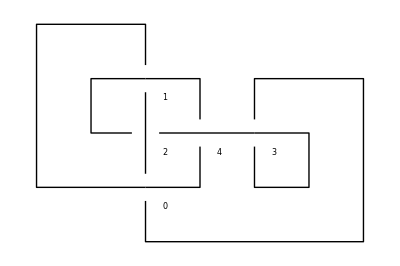

```mathematica
PlotDiagram[PlanarDiagram[Import[childrensgamefiles[[2]]]]]
```

```mathematica
cgknots = PlanarDiagram[Import[Echo[#]]]&/@ childrensgamefiles
```

/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-01.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-02.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-03.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-04.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-05.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-06.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-07.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-08.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-09.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-10.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-11.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-12.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-13.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-14.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-15.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-16.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-17.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-18.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-19.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-20.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-21.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-22.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-23.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-24.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-25.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-26.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-27.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-28.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-29.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-30.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-31.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-32.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-33.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-34.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-35.tsv

/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-36.tsv

LibraryFunction::noinst: Managed library expression instance does not exist.

General::stop: Further output of LibraryFunction::noinst will be suppressed during this calculation.

{PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…],PlanarDiagramObject[…]}